# Symbolic Regression of Pendulum Data

## Introduction

## Lagrangians

### Euler Lagrange Equations

### Converting Expression from Cloure.

## Single Pendulum

### Theoretical Lagrangian

Theoretical single pendulum Lagrangian is of the form:

(L=1/2 mr^2(dθ/dt))^2-mgr(1-cosθ)

```mathematica
mass=1
length=1
gravity=1

simplepenlag[theta_,thetaprime_]:=(1/2*mass*length^2*thetaprime^2)-mass*gravity*length*(1-Cos[theta])
```

1

1

1

```mathematica
singpendata = Import["/Users/joelrussell/Documents/Imperial/Year_4/Masters_Project/Code/joel_flow/flow/data/mma_pendulum_large.csv"] //Short

theta={#⟦1⟧&/@singpendata} 
thetaprime={#⟦2⟧&/@singpendata}
```

(«1»)

{{2.98451,-2.71051×10^-20}}

{{2.98137,-0.0629866}}

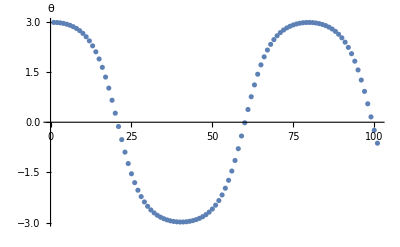

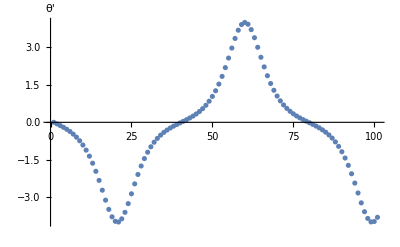

```mathematica
ListPlot[theta,AxesLabel->θ]
ListPlot[thetaprime,AxesLabel->θ']
```

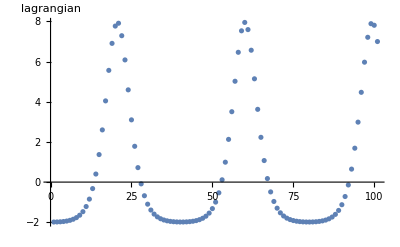

```mathematica
ListPlot[simplepenlag[theta,thetaprime],AxesLabel->lagrangian]
```

### Numerical Lagrangian Expressions

```mathematica
triallag1[theta_,omega_]:=Times[Times[0.022210588271571317, Plus[Plus[Plus[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Times[Cos[theta], 0.6247552574671112]], Cos[theta]], Times[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]]], omega], omega], Cos[theta]]], Sin[theta]]
```

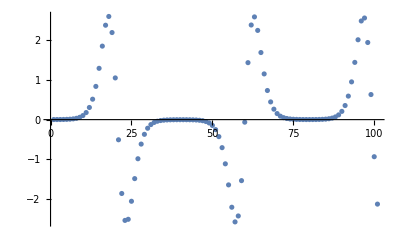

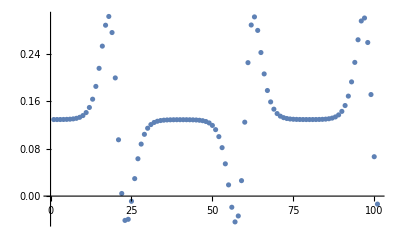

```mathematica
run1[theta_,omega_]:=Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12642579887098596], Times[omega, omega]]]]
run2[theta_,omega_]:=Times[Plus[Plus[Sin[theta], Subtract[Plus[Sin[theta], 1.9273329585287498], Sin[theta]]], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12641372676463694], Times[omega, omega]]]], 0.06703977631709543]

ListPlot[run1[theta,thetaprime]]
ListPlot[run2[theta,thetaprime]]
```

### Euler Lagrange Equations

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
"
theorysoln = θ[t]/.theorysoln/.{C[1]→1,C[2]→1}

NDSolve[Join[myEq, {\theta[0] == 1.5, \theta'[0] == 0.0}, {\theta[t]}, {t, 0, 10}]"
```

theorysoln = θ[t]/.theorysoln/.{C[1]→1,C[2]→1}

NDSolve[Join[myEq, {	heta[0] == 1.5, 	heta'[0] == 0.0}, {	heta[t]}, {t, 0, 10}]

#### THEORETICAL

1

1

9.81

Theoretical Values with Algebraic Representations of m g and l

mgr (1-cos(θ(t)))+1/2 mr^2 (θ'(t))^2

mgr sin(θ(t))-mr^2 θ''(t)==0

{{θ''(t)→(mgr sin(θ(t)))/mr^2}}

1/2 (θ'(t))^2+9.81 (1-cos(θ(t)))

9.81 sin(θ(t))-θ''(t)==0

{9.81 sin(θ(t))-θ''(t)==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

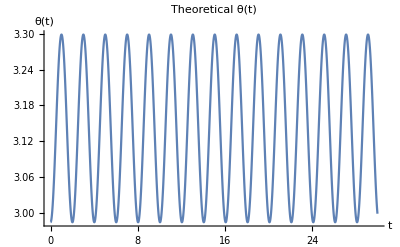

```mathematica
Clear[m,l,g]

m = 1
l = 1
g = 9.81

"Theoretical Values with Algebraic Representations of m g and l"

theorylag = 1/2 mr^2 θ'[t]^2+mgr(1-Cos[θ[t]])
theoryEL = EulerEquations[theorylag,θ[t],t]
theorysol = Solve[theoryEL,θ''[t]]


theorylagn = 1/2 m*l^2*θ'[t]^2+m*g*l*(1-Cos[θ[t]])
ELth = EulerEquations[theorylagn,θ[t],t]

s =Join[List[ELth],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

theorysoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.theorysoln],{t,0,30},PlotRange->All,PlotLabel->Theoretical θ[t],AxesLabel->{t,θ[t]}]
```

```mathematica
"theorylag[mass_,length_,gravity_] := 1/2mass*length^2*"
```

theorylag[mass_,length_,gravity_] := 1/2mass*length^2*

#### EXPERIMENTAL

0.0670398 (0.126401 omega^2 sin(theta)+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 sin(theta) (θ'(t))^2+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 (θ'(t))^2 sin(θ(t))+sin(θ(t))+sin(θ(t)) cos(θ(t)))

-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0

{-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

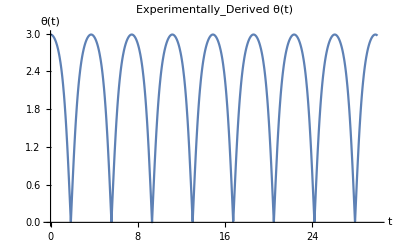

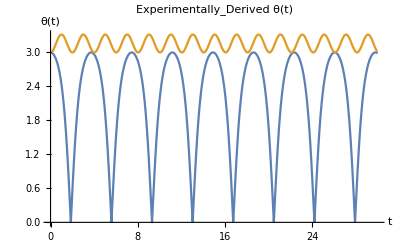

```mathematica
Clear[theta]

L= Times[Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.1264012221818857], Times[omega, omega]]]], 0.06703977631709543]

L = L/.omega->θ'[t]
L = L/.theta->θ[t]

ELexp = EulerEquations[L,θ[t],t]

Clear[s]

s =Join[List[ELexp],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

expsoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.expsoln],{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

```mathematica
Plot[{Evaluate[θ[t]/.expsoln], Evaluate[θ[t]/.theorysoln]},{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

-Graphics-

## Double Pendulum

```mathematica
Simplify[Times[Times[Times[Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[Times[Times[theta2, theta2], Times[theta1, theta1]], Times[Times[Cos[omega1], Times[theta1, theta1]], Times[theta1, theta1]]]]], Times[theta1, theta1]], Times[Times[Times[theta2, theta2], Subtract[Sin[theta1], theta1]], Cos[omega2]]], Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[theta1, theta1]]]]]
```

theta1^10 theta2^12 cos(omega1) cos(omega2) (sin(theta1)-theta1)